-2.01

0.9

16.3052/x^2.91

16.3052/x^2.91

16.3052/x^2.91

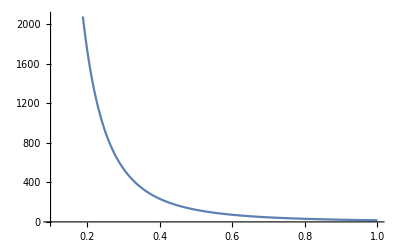

-Graphics-

-Graphics-

```mathematica
Clear[x,k,alpha]
k = -2.01
alpha = 0.9
s1=Gamma[1+k]/Gamma[1+k-alpha]x ^(k-alpha)
s2=ResourceFunction["FractionalOrderD"][x^k,{x,alpha}]
s3=FractionalD[x^k,{x,alpha}]
Plot[s1,{x,0.1,1}]
Plot[s2,{x,0.1,1}]
Plot[s3,{x,0.1,1}]
```